## UNDAMPED

```mathematica
W[x_]:=c1 Cos[β x]+c2 Sin[β x]+c3 Cosh[β x]+c4 Sinh[β x]
```

```mathematica
eq1=W[0]
```

c1+c3

```mathematica
D[W[x],{x,2}]
```

-c1 β^2 Cos[x β]+c3 β^2 Cosh[x β]-c2 β^2 Sin[x β]+c4 β^2 Sinh[x β]

```mathematica
W2[x_]:=-c1 β^2 Cos[x β]+c3 β^2 Cosh[x β]-c2 β^2 Sin[x β]+c4 β^2 Sinh[x β]
```

```mathematica
eq2=W2[0]
```

-c1 β^2+c3 β^2

```mathematica
sol=Solve[{eq1,eq2}==0,{c1,c3}][[1]]
```

{c1→0,c3→0}

```mathematica
eq3=W[L]/.sol
```

c2 Sin[L β]+c4 Sinh[L β]

```mathematica
eq4=W2[L]/.sol
```

-c2 β^2 Sin[L β]+c4 β^2 Sinh[L β]

```mathematica
Matrix1={{Sin[β L],Sinh[β L]},{-β^2 Sin[β L],β^2 Sinh[β L]}};MatrixForm@Matrix1
```

(Sin[L β] | Sinh[L β]
-β^2 Sin[L β] | β^2 Sinh[L β])

```mathematica
Determinant=Det@Matrix1
```

2 β^2 Sin[L β] Sinh[L β]

```mathematica
Reduce[Determinant==0,β]
```

(C[1]∈ℤ&&L≠0&&(β==(2 ⅈ π C[1])/L||β==(2 π C[1])/L||β==(ⅈ π+2 ⅈ π C[1])/L||β==(π+2 π C[1])/L))||L==0||β==0

```mathematica
sol1=MatrixForm[(Matrix1/.β->(Pi/L)) . {c2,c4}]
```

(c4 Sinh[π]
(c4 π^2 Sinh[π])/L^2)

```mathematica
e1=c2 Sin[L (Pi/L)]+c4 Sinh[L (Pi/L)];e2=-c2 π^2 Sin[L (Pi/L)]+c4 π^2 Sinh[L (Pi/L)];
Solve[{e1,e2}==0,{c2,c4}]
```

{{c4→0}}

```mathematica
sol2=MatrixForm[(Matrix1/.β->(2Pi/L)) . {c2,c4}]
```

(c4 Sinh[2 π]
(4 c4 π^2 Sinh[2 π])/L^2)

```mathematica
e3=c2 Sin[L(2Pi/L)]+c4 Sinh[L(2Pi/L)];e4=-4 c2 π^2 Sin[L(2Pi/L)]+4 c4 π^2 Sinh[L(2Pi/L)];
Solve[{e3,e4}==0,{c2,c4}]
```

{{c4→0}}

```mathematica
sol3=MatrixForm[(Matrix1/.β->(3Pi/L)) . {c2,c4}]
```

(c4 Sinh[3 π]
(9 c4 π^2 Sinh[3 π])/L^2)

#### Natural frequencies

```mathematica
Emod=206*10^9;J=6370*10^{-12};ρ=7850;A=111*10^{-6};c=N@√((Emod*J)/(ρ*A))
```

{38.8067}

```mathematica
β1=Pi/L
β2=(2Pi)/L
β3=(3Pi)/L
```

π/L

(2 π)/L

(3 π)/L

```mathematica
L=0.7;
```

```mathematica
w1=(β1^2*c)
w2=(β2^2*c)
w3=(β3^2*c)
```

{781.647}

{3126.59}

{7034.82}

```mathematica
w1=(β1^2*c)/6.28
w2=(β2^2*c)/6.28
w3=(β3^2*c)/6.28
```

{124.466}

{497.864}

{1120.19}

#### Mode shapes

```mathematica
W1=c21 Sin[β1 x];W2=c22 Sin[β2 x];W3=c23 Sin[β3 x];
```

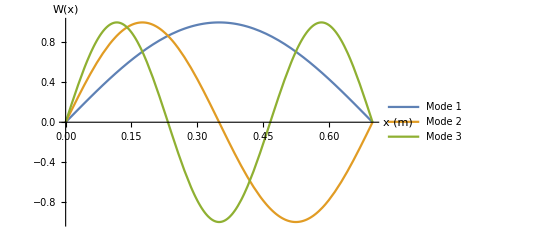

```mathematica
Block[{c21=1,c22=1,c23=1},
Plot[{W1,W2,W3},{x,0,L},PlotLegends->{"Mode 1","Mode 2","Mode 3"},AxesLabel->{"x (m)","W(x)"}]]
```

#### Transfer function

```mathematica
b1=Integrate[W1^2,{x,0,L}];b2=b1/.c21->c22;b3=b1/.c21->c23;
```

```mathematica
EqdUndamped=qn''[t]+wn^2 qn[t]==((DiracDelta[t]*Wn[x0])/(ρ*A*bn))[[1]]
```

wn^2 qn[t]+qn''[t]==(20000 DiracDelta[t] Wn[x0])/(17427 bn)

```mathematica
SoldUndamped=FullSimplify@DSolve[{EqdUndamped},qn[t],t]/.HeavisideTheta[t]->1/.C[1]->Cn/.C[2]->Dn
```

{{qn[t]→Cn Cos[t wn]+Dn Sin[t wn]+(20000 Sin[t wn] Wn[x0])/(17427 bn wn)}}

```mathematica
q=qn[t]/.SoldUndamped[[1,1]];
```

```mathematica
solutionsUndamped=SoldUndamped[[1,1]]
```

qn[t]→Cn Cos[t wn]+Dn Sin[t wn]+(20000 Sin[t wn] Wn[x0])/(17427 bn wn)

```mathematica
q1=qn[t]/.solutionsUndamped/.bn->b1/.wn->w1/.Wn[x0]->c21*Sin[π/8]/.c21->1
```

{Cn Cos[124.466 t]+0.0100816 Sin[124.466 t]+Dn Sin[124.466 t]}

```mathematica
q2=qn[t]/.solutionsUndamped/.bn->b2/.wn->w2/.Wn[x0]->c22*Sin[π/4]/.c22->1
```

{Cn Cos[497.864 t]+0.00465708 Sin[497.864 t]+Dn Sin[497.864 t]}

```mathematica
q3=qn[t]/.solutionsUndamped/.bn->b3/.wn->w3/.Wn[x0]->c23*Sin[(3π)/8]/.c23->1
```

{Cn Cos[1120.19 t]+0.00270434 Sin[1120.19 t]+Dn Sin[1120.19 t]}

```mathematica
w=W1*q1+W2*q2+W3*q3/.c21->1/.c22->1/.c23->1
```

{(Cn Cos[124.466 t]+0.0100816 Sin[124.466 t]+Dn Sin[124.466 t]) Sin[4.48799 x]+(Cn Cos[497.864 t]+0.00465708 Sin[497.864 t]+Dn Sin[497.864 t]) Sin[8.97598 x]+(Cn Cos[1120.19 t]+0.00270434 Sin[1120.19 t]+Dn Sin[1120.19 t]) Sin[13.464 x]}

```mathematica
LaplaceUndamped=LaplaceTransform[D[w/.c21->1/.c22->1/.c23->1/.ϕ1->0/.ϕ2->0/.ϕ3->0/.x->(L/2),{t,2}],t,s][[1]]
```

-19439.3/(15491.8+s^2)-(1.9282×10^6 Dn)/(15491.8+s^2)-(15491.8 Cn s)/(15491.8+s^2)-(7.03813×10^-11)/(247869.+s^2)-(1.51128×10^-8 Dn)/(247869.+s^2)-(3.03552×10^-11 Cn s)/(247869.+s^2)+(3.80138×10^6)/(1.25484×10^6+s^2)+(1.40566×10^9 Dn)/(1.25484×10^6+s^2)+(1.25484×10^6 Cn s)/(1.25484×10^6+s^2)

```mathematica
AbsTF=Abs[LaplaceUndamped/.s->(ⅈ*freq)];
```

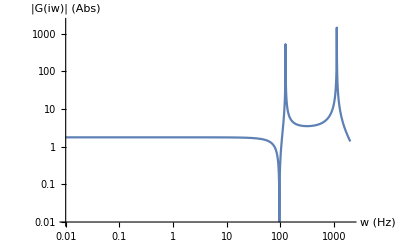

```mathematica
LogLogPlot[AbsTF/.Cn->0/.Dn->0,{freq,0.01,2000},PlotRange->{{0.01,2000},{0.01,2000}},AxesLabel->{"w (Hz)","|G(iw)| (Abs)"}(*, PlotLegends->{"Undamped case"}*)]
```

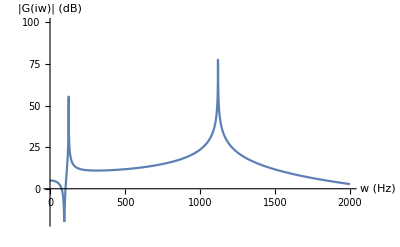

```mathematica
Plot[20*Log10[ AbsTF]/.Cn->0/.Dn->0,{freq,0,2000},PlotRange->{{0,2000},{-20,100}},(*,PlotLegends->{"Damped case"}*)AxesLabel->{"w (Hz)","|G(iw)| (dB)"}]
```

## DAMPED

```mathematica
chi1=0.05;chi2=0.01;chi3=0.01;
```

```mathematica
W1
```

c21 Sin[4.48799 x]

```mathematica
b1=Integrate[W1^2,{x,0,L}]
```

0.35 c21^2

```mathematica
b2=b1/.c21->c22;
b3=b1/.c21->c23;
```

#### General modal oscillator with damping - Differential equation

```mathematica
Eqd=qn''[t]+2 ξn wn qn'[t]+wn^2 qn[t]==((DiracDelta[t]*Wn[x0])/(ρ*A*bn))[[1]]
```

wn^2 qn[t]+2 wn ξn qn'[t]+qn''[t]==(20000 DiracDelta[t] Wn[x0])/(17427 bn)

```mathematica
Sold=FullSimplify@DSolve[{Eqd},qn[t],t]/.HeavisideTheta[t]->1/.C[1]->Cn/.C[2]->Dn
```

{{qn[t]→(ⅇ^(-t (wn ξn+√(wn^2 (-1+ξn^2)))) (17427 bn (Cn+Dn ⅇ^(2 t √(wn^2 (-1+ξn^2)))) wn^2 (-1+ξn^2)+10000 (-1+ⅇ^(2 t √(wn^2 (-1+ξn^2)))) √(wn^2 (-1+ξn^2)) Wn[x0]))/(17427 bn wn^2 (-1+ξn^2))}}

```mathematica
q=qn[t]/.Sold[[1,1]]
```

(ⅇ^(-t (wn ξn+√(wn^2 (-1+ξn^2)))) (17427 bn (Cn+Dn ⅇ^(2 t √(wn^2 (-1+ξn^2)))) wn^2 (-1+ξn^2)+10000 (-1+ⅇ^(2 t √(wn^2 (-1+ξn^2)))) √(wn^2 (-1+ξn^2)) Wn[x0]))/(17427 bn wn^2 (-1+ξn^2))

For t  > 0 , HeavisideTheta[t] = 1

```mathematica
solutions=Sold[[1,1]]
```

qn[t]→(ⅇ^(-t (wn ξn+√(wn^2 (-1+ξn^2)))) (17427 bn (Cn+Dn ⅇ^(2 t √(wn^2 (-1+ξn^2)))) wn^2 (-1+ξn^2)+10000 (-1+ⅇ^(2 t √(wn^2 (-1+ξn^2)))) √(wn^2 (-1+ξn^2)) Wn[x0]))/(17427 bn wn^2 (-1+ξn^2))

```mathematica
q1=qn[t]/.solutions/.bn->b1/.wn->w1/.ξn->chi1/.Wn[x0]->c21*Sin[π/8]/.c21->1
```

{-1.06095×10^-8 ⅇ^((-6.2233-124.31 ⅈ) t) ((0.+475715. ⅈ) (-1+ⅇ^((0.+248.621 ⅈ) t))-9.42553×10^7 (Cn+Dn ⅇ^((0.+248.621 ⅈ) t)))}

```mathematica
q2=qn[t]/.solutions/.bn->b2/.wn->w2/.ξn->chi2/.Wn[x0]->c22*Sin[π/4]/.c22->1
```

{-6.61501×10^-10 ⅇ^((-4.97864-497.839 ⅈ) t) ((0.+3.52026×10^6 ⅈ) (-1+ⅇ^((0.+995.679 ⅈ) t))-1.51171×10^9 (Cn+Dn ⅇ^((0.+995.679 ⅈ) t)))}

```mathematica
q3=qn[t]/.solutions/.bn->b3/.wn->w3/.ξn->chi3/.Wn[x0]->c23*Sin[(3π)/8]/.c23->1
```

{-1.30667×10^-10 ⅇ^((-11.2019-1120.14 ⅈ) t) ((0.+1.03487×10^7 ⅈ) (-1+ⅇ^((0.+2240.28 ⅈ) t))-7.65305×10^9 (Cn+Dn ⅇ^((0.+2240.28 ⅈ) t)))}

#### Transfer function

```mathematica
Wn=Sin[βn x] (* Generic solution in space *)
```

Sin[x βn]

```mathematica
w=W1*q1+W2*q2+W3*q3/.c21->1/.c22->1/.c23->1
```

{-1.06095×10^-8 ⅇ^((-6.2233-124.31 ⅈ) t) ((0.+475715. ⅈ) (-1+ⅇ^((0.+248.621 ⅈ) t))-9.42553×10^7 (Cn+Dn ⅇ^((0.+248.621 ⅈ) t))) Sin[4.48799 x]-6.61501×10^-10 ⅇ^((-4.97864-497.839 ⅈ) t) ((0.+3.52026×10^6 ⅈ) (-1+ⅇ^((0.+995.679 ⅈ) t))-1.51171×10^9 (Cn+Dn ⅇ^((0.+995.679 ⅈ) t))) Sin[8.97598 x]-1.30667×10^-10 ⅇ^((-11.2019-1120.14 ⅈ) t) ((0.+1.03487×10^7 ⅈ) (-1+ⅇ^((0.+2240.28 ⅈ) t))-7.65305×10^9 (Cn+Dn ⅇ^((0.+2240.28 ⅈ) t))) Sin[13.464 x]}

```mathematica
w/.t->0
```

{(-1.06095×10^-8+0. ⅈ) ((0.+0. ⅈ)-9.42553×10^7 (Cn+(1.+0. ⅈ) Dn)) Sin[4.48799 x]-(6.61501×10^-10+0. ⅈ) ((0.+0. ⅈ)-1.51171×10^9 (Cn+(1.+0. ⅈ) Dn)) Sin[8.97598 x]-(1.30667×10^-10+0. ⅈ) ((0.+0. ⅈ)-7.65305×10^9 (Cn+(1.+0. ⅈ) Dn)) Sin[13.464 x]}

```mathematica
Cn1=2/L∫_0^L (w/.t->0)*Wnⅆx
```

{2.85714 (Cn+1. Dn) (-(0.5 Sin[3.14159-0.7 βn])/(-4.48799+1. βn)-(0.5 Sin[6.28319-0.7 βn])/(-8.97598+1. βn)-(0.5 Sin[9.42478-0.7 βn])/(-13.464+1. βn)-(0.5 Sin[0.7 (4.48799+βn)])/(4.48799+βn)-(0.5 Sin[0.7 (8.97598+βn)])/(8.97598+βn)-(0.5 Sin[0.7 (13.464+βn)])/(13.464+βn))}

```mathematica
Dn1=2/(L*wn)∫_0^L (w/.t->0)*Wnⅆx
```

{(2.85714 (Cn+1. Dn) (-(0.5 Sin[3.14159-0.7 βn])/(-4.48799+1. βn)-(0.5 Sin[6.28319-0.7 βn])/(-8.97598+1. βn)-(0.5 Sin[9.42478-0.7 βn])/(-13.464+1. βn)-(0.5 Sin[0.7 (4.48799+βn)])/(4.48799+βn)-(0.5 Sin[0.7 (8.97598+βn)])/(8.97598+βn)-(0.5 Sin[0.7 (13.464+βn)])/(13.464+βn)))/wn}

```mathematica
w/.x->(L/2)
```

{-1.06095×10^-8 ⅇ^((-6.2233-124.31 ⅈ) t) ((0.+475715. ⅈ) (-1+ⅇ^((0.+248.621 ⅈ) t))-9.42553×10^7 (Cn+Dn ⅇ^((0.+248.621 ⅈ) t)))-8.10105×10^-26 ⅇ^((-4.97864-497.839 ⅈ) t) ((0.+3.52026×10^6 ⅈ) (-1+ⅇ^((0.+995.679 ⅈ) t))-1.51171×10^9 (Cn+Dn ⅇ^((0.+995.679 ⅈ) t)))+1.30667×10^-10 ⅇ^((-11.2019-1120.14 ⅈ) t) ((0.+1.03487×10^7 ⅈ) (-1+ⅇ^((0.+2240.28 ⅈ) t))-7.65305×10^9 (Cn+Dn ⅇ^((0.+2240.28 ⅈ) t)))}

```mathematica
test=D[w/.x->(L/2),{t,2}]
```

{(1.32052×10^-7+2.63774×10^-6 ⅈ) ⅇ^((-6.2233-124.31 ⅈ) t) ((-1.18273×10^8+0. ⅈ) ⅇ^((0.+248.621 ⅈ) t)-(0.+2.34338×10^10 ⅈ) Dn ⅇ^((0.+248.621 ⅈ) t))-1.06095×10^-8 ⅇ^((-6.2233-124.31 ⅈ) t) ((0.-2.94051×10^10 ⅈ) ⅇ^((0.+248.621 ⅈ) t)+(5.82614×10^12+0. ⅈ) Dn ⅇ^((0.+248.621 ⅈ) t))+(8.06645×10^-25+8.06605×10^-23 ⅈ) ⅇ^((-4.97864-497.839 ⅈ) t) ((-3.50505×10^9+0. ⅈ) ⅇ^((0.+995.679 ⅈ) t)-(0.+1.50518×10^12 ⅈ) Dn ⅇ^((0.+995.679 ⅈ) t))-8.10105×10^-26 ⅇ^((-4.97864-497.839 ⅈ) t) ((0.-3.4899×10^12 ⅈ) ⅇ^((0.+995.679 ⅈ) t)+(1.49868×10^15+0. ⅈ) Dn ⅇ^((0.+995.679 ⅈ) t))-(2.92745×10^-9+2.9273×10^-7 ⅈ) ⅇ^((-11.2019-1120.14 ⅈ) t) ((-2.3184×10^10+0. ⅈ) ⅇ^((0.+2240.28 ⅈ) t)-(0.+1.71449×10^13 ⅈ) Dn ⅇ^((0.+2240.28 ⅈ) t))+1.30667×10^-10 ⅇ^((-11.2019-1120.14 ⅈ) t) ((0.-5.19387×10^13 ⅈ) ⅇ^((0.+2240.28 ⅈ) t)+(3.84094×10^16+0. ⅈ) Dn ⅇ^((0.+2240.28 ⅈ) t))+(0.000163538-0.0000164155 ⅈ) ⅇ^((-6.2233-124.31 ⅈ) t) ((0.+475715. ⅈ) (-1+ⅇ^((0.+248.621 ⅈ) t))-9.42553×10^7 (Cn+Dn ⅇ^((0.+248.621 ⅈ) t)))+(2.0076×10^-20-4.0158×10^-22 ⅈ) ⅇ^((-4.97864-497.839 ⅈ) t) ((0.+3.52026×10^6 ⅈ) (-1+ⅇ^((0.+995.679 ⅈ) t))-1.51171×10^9 (Cn+Dn ⅇ^((0.+995.679 ⅈ) t)))-(0.000163933-3.27915×10^-6 ⅈ) ⅇ^((-11.2019-1120.14 ⅈ) t) ((0.+1.03487×10^7 ⅈ) (-1+ⅇ^((0.+2240.28 ⅈ) t))-7.65305×10^9 (Cn+Dn ⅇ^((0.+2240.28 ⅈ) t)))}

```mathematica
laplace=LaplaceTransform[test,t,s][[1]]
```

-(1.41366×10^-15-7.06726×10^-14 ⅈ)/((4.97864-497.839 ⅈ)+1. s)-((3.03491×10^-11+6.07073×10^-13 ⅈ) Dn)/((4.97864-497.839 ⅈ)+1. s)-(1.41366×10^-15+7.06726×10^-14 ⅈ)/((4.97864+497.839 ⅈ)+1. s)-((3.03491×10^-11-6.07073×10^-13 ⅈ) Cn)/((4.97864+497.839 ⅈ)+1. s)-(7.80908-77.7977 ⅈ)/((6.2233-124.31 ⅈ)+1. s)-((15414.3+1547.24 ⅈ) Dn)/((6.2233-124.31 ⅈ)+1. s)-(7.80908+77.7977 ⅈ)/((6.2233+124.31 ⅈ)+1. s)-((15414.3-1547.24 ⅈ) Cn)/((6.2233+124.31 ⅈ)+1. s)+(33.935-1696.5 ⅈ)/((11.2019-1120.14 ⅈ)+1. s)+((1.25459×10^6+25095.5 ⅈ) Dn)/((11.2019-1120.14 ⅈ)+1. s)+(33.935+1696.5 ⅈ)/((11.2019+1120.14 ⅈ)+1. s)+((1.25459×10^6-25095.5 ⅈ) Cn)/((11.2019+1120.14 ⅈ)+1. s)

```mathematica
Gan=laplace/.s->(ⅈ*freq) (* freq is the frequency w *)
```

-(1.41366×10^-15-7.06726×10^-14 ⅈ)/((4.97864-497.839 ⅈ)+(0.+1. ⅈ) freq)-((3.03491×10^-11+6.07073×10^-13 ⅈ) Dn)/((4.97864-497.839 ⅈ)+(0.+1. ⅈ) freq)-(1.41366×10^-15+7.06726×10^-14 ⅈ)/((4.97864+497.839 ⅈ)+(0.+1. ⅈ) freq)-((3.03491×10^-11-6.07073×10^-13 ⅈ) Cn)/((4.97864+497.839 ⅈ)+(0.+1. ⅈ) freq)-(7.80908-77.7977 ⅈ)/((6.2233-124.31 ⅈ)+(0.+1. ⅈ) freq)-((15414.3+1547.24 ⅈ) Dn)/((6.2233-124.31 ⅈ)+(0.+1. ⅈ) freq)-(7.80908+77.7977 ⅈ)/((6.2233+124.31 ⅈ)+(0.+1. ⅈ) freq)-((15414.3-1547.24 ⅈ) Cn)/((6.2233+124.31 ⅈ)+(0.+1. ⅈ) freq)+(33.935-1696.5 ⅈ)/((11.2019-1120.14 ⅈ)+(0.+1. ⅈ) freq)+((1.25459×10^6+25095.5 ⅈ) Dn)/((11.2019-1120.14 ⅈ)+(0.+1. ⅈ) freq)+(33.935+1696.5 ⅈ)/((11.2019+1120.14 ⅈ)+(0.+1. ⅈ) freq)+((1.25459×10^6-25095.5 ⅈ) Cn)/((11.2019+1120.14 ⅈ)+(0.+1. ⅈ) freq)

```mathematica
Gtest=Abs[Gan];
```

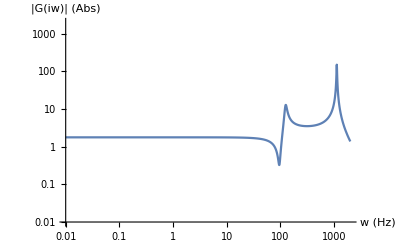

```mathematica
LogLogPlot[Gtest/.Cn->0/.Dn->0,{freq,0.01,2000},PlotRange->{{0.01,2000},{0.01,2000}},(*,PlotLegends->{"Damped case"}*)AxesLabel->{"w (Hz)","|G(iw)| (Abs)"}]
```

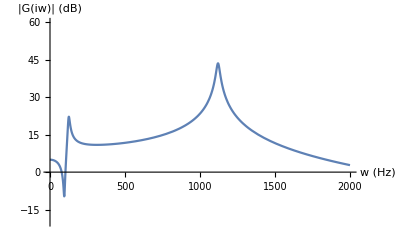

```mathematica
Plot[20*Log10[ Gtest]/.Cn->0/.Dn->0,{freq,0,2000},PlotRange->{{0,2000},{-20,60}},AxesLabel->{"w (Hz)","|G(iw)| (dB)"}]
```